Equation: 0.+Sin[x] u[x]+Sin[x] u''[x]==1.

Boundary conditions: {u[0]==0,u[1]==1}

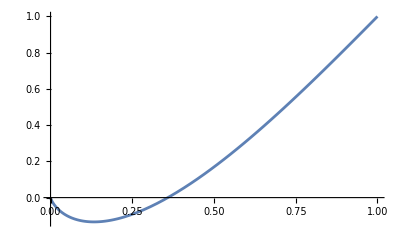

```mathematica
Clear["Global`*"]
d[x_]:=-N[Sin[x]];
b[x_]:=-Cos[x]//N;
c[x_]:=Sin[x]//N;
f[x_]:=1//N;

alpha=0;
beta=1;
mu0=0;
mu1=1;
mu=2.40483;

n=25;
h=(beta-alpha)/(n+1);
eq=-D[(d[x]*u'[x]),x]+b[x]*u'[x]+c[x]*u[x]==f[x];
bc={u[alpha]==mu0,u[beta]==mu1};
Print["Equation: ",eq];
Print["Boundary conditions: ",bc];
ua=Quiet@NDSolveValue[{eq,bc},u,{x,alpha,beta}];
Print[Show[Plot[{ua[x]},{x,alpha,beta}]]]
xgrid=Table[alpha+h*i,{i,0,n}];
As=Table[0,{i,1,n+1},{j,1,n+1}];
Ac=Table[0,{i,1,n+1},{j,1,n+1}];
Am=Table[0,{i,1,n+1},{j,1,n+1}];
fv=Table[0,{i,1,n+1}];
For[i=2,i<n,i++,
Napp=a0+a1*x;
(*eq3=Napp/.{x->xgrid[[i-1]]};*)
eq1=Napp/.{x->xgrid[[i]]};
eq2=Napp/.{x->xgrid[[i+1]]};
sol=Solve[{eq1==x1,eq2==x2},{a0,a1}];
Napp=Napp/.sol[[1]];
(*N3=Coefficient[Napp,x3];*)
N1=Coefficient[Napp,x1];
N2=Coefficient[Napp,x2];
Ni={{N1,N2}};
(*Print[Ni//MatrixForm];*)
(*Print[(Transpose[Ni].Ni)//MatrixForm];*)
dNi=D[Ni,x];
Ase=NIntegrate[d[x]*Transpose[dNi].dNi,{x,xgrid[[i]],xgrid[[i+1]]}];
(*Print[Integrate[Transpose[dNi].dNi,{x,xgrid[[i]],xgrid[[i+1]]}](-xgrid[[i]]+xgrid[[i+1]])//MatrixForm];*)
Ace=NIntegrate[b[x]*Transpose[Ni].dNi,{x,xgrid[[i]],xgrid[[i+1]]}];
(*Print[Integrate[Transpose[Ni].dNi,{x,xgrid[[i]],xgrid[[i+1]]}]*2//MatrixForm];*)
Ame=NIntegrate[c[x]*Transpose[Ni].Ni,{x,xgrid[[i]],xgrid[[i+1]]}];
(*Print[Integrate[Transpose[Ni].Ni,{x,xgrid[[i]],xgrid[[i+1]]}]*6/(-xgrid[[i]]+xgrid[[i+1]])//MatrixForm];*)
fve=NIntegrate[f[x]*Transpose[Ni],{x,xgrid[[i]],xgrid[[i+1]]}];
(*Print[fve//MatrixForm];*)
Do[
As[[i+j,i+k]]+=Ase[[j+1,k+1]];
Ac[[i+j,i+k]]+=Ace[[j+1,k+1]];
Am[[i+j,i+k]]+=Ame[[j+1,k+1]],
{j,0,1},{k,0,1}];
Do[
fv[[i+j]]+=fve[[j+1,1]]//N,
{j,0,1}];
];
A=(As+Ac+Am);
A[[1,1]]=A[[n+1,n+1]]=1;
fv[[1]]+=mu0;fv[[n+1]]+=mu1;
A[[2,2]]+=d[alpha+h/2]/h+b[alpha+h/2]/2+c[alpha+h/2]/3*h;
A[[n,n]]+=d[beta-h/2]/h-b[beta-h/2]/2+c[beta-h/2]/3*h;
fv[[2]]+=f[alpha]*h;
fv[[n]]+=f[beta]*h+ d[beta-h/2]/h-b[beta-h/2]/2+c[beta-h/2]/3*h;
(*Print[A//MatrixForm,fv//MatrixForm];*)
sole=LinearSolve[A,fv];
```

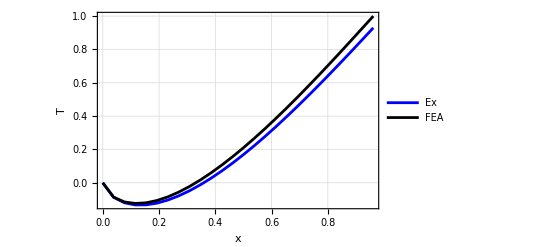

```mathematica
Show[ListLinePlot[{Table[{xgrid[[i]],ua[xgrid[[i]]]},{i,1,Length[xgrid]}],Table[{xgrid[[i]],sole[[i]]},{i,1,Length[xgrid]}]},
PlotStyle->{Blue,Black},FrameStyle->Directive[Black,12],
PlotRange->All,Frame->True,FrameLabel->{Style["x",16,Black,FontFamily->"Cambria"],Style["T",16,Black,FontFamily->"Cambria"]},
GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotRange->All,
PlotLegends->Placed[{Style["Ex",16,Black,FontFamily->"Cambria"],Style["FEA",16,Black,FontFamily->"Cambria"]},Right]]
]
```

```mathematica
(*phiI[x_,i_]:=Piecewise[{
{(x-xgrid[[i-1]])/(xgrid[[i]]-xgrid[i-1]]),xgrid[[i-1]]<=x<=xgrid[[i]]},
{(xgrid[[i+1]]-x)/(xgrid[[i+1]]-xgrid[[i]]),xgrid[[i]]<=x<=xgrid[[i+1]]},
{0}
}];
As=Table[0,{i,1,n+1},{j,1,n+1}];
Ac=Table[0,{i,1,n+1},{j,1,n+1}];
Am=Table[0,{i,1,n+1},{j,1,n+1}];
Do[
hi=xgrid[[i+1]]-xgrid[[i]];
xih=(xgrid[[i+1]]+xgrid[[i]])/2;
Ase=d[alpha+xih]/hi*{{1,-1},{-1,1}};
Ace=b[alpha+xih]/2*{{-1,-1},{1,1}};
Ame=c[alpha+xih]/6*{{2,1},{1,2}};
Do[
As[[i+j,i+k]]+=Ase[[j+1,k+1]];
Ac[[i+j,i+k]]+=Ace[[j+1,k+1]];
Am[[i+j,i+k]]+=Ame[[j+1,k+1]],
{j,0,1},{k,0,1}],

{i,2,n-1}];
A=As+Ac+Am;
Print[N[A//MatrixForm]];
A[[1,1]]=A[[n+1,n+1]]=1;
A[[2,2]]+=d[alpha+h/2]/h+b[alpha+h/2]/2+c[alpha+h/2]/3;
A[[n,n]]+=d[beta-h/2]/h+b[beta-h/2]/2+c[beta-h/2]/3;
fv=Table[0,{i,1,n+1}];
Do[
,{}]*)
```